```mathematica
(* Probability of violating the bounds - saturation SDIS *)
```

```mathematica
fvp[pv_,F_]:=pv/2+(1-pv)*(pv^2*F/4+(1-pv^2)*F/3)
```

```mathematica
(* Evolution of the violation probability *)
```

```mathematica
evolViolationProb[pv0_,F_,gen_]:=Module[{pvList={pv0}},Do[pvList=Append[pvList,fvp[Last[pvList],F]],{gen}]; Return[pvList]]
```

```mathematica
(* values of the scale factor used in the experimental analysis *)
```

```mathematica
listF={0.05,0.285,0.52,0.755,0.99};
```

```mathematica
(* color map for plots *)
```

```mathematica
colors={{0.4,0.7607843137254902,0.6470588235294118},{0.9882352941176471,0.5529411764705883,0.3843137254901961},{0.5529411764705883,0.6274509803921569,0.796078431372549},{0.9058823529411765,0.5411764705882353,0.7647058823529411},{0.6509803921568628,0.8470588235294118,0.32941176470588235},{0.8980392156862745,0.7686274509803922,0.5803921568627451}};
```

```mathematica
gen=100;
gLines=Table[Plot[listF[[indF]]/3,{g,1,gen},Frame->True,FrameLabel->{"generation","Bound violation probability"},GridLines->Automatic,PlotStyle->{Dashed, RGBColor[colors[[Length[listF]-indF+1]]]},PlotRange->{{1,gen/2},{0,0.6}}],{indF,Length[listF],1,-1}];
gSaturation=ListLinePlot[Table[evolViolationProb[listF[[indF]]/3,listF[[indF]],gen],{indF,Length[listF],1,-1 }],Frame->True,FrameLabel->{"generation","Bound violation probability"},PlotStyle->Map[RGBColor,colors],PlotRange->{{1,gen},{0,0.6}},GridLines->Automatic,PlotLegends->Placed[{"F=0.99","F=0.75","F=0.52","F=0.285","F=0.05"},{Right,Top}]];
```

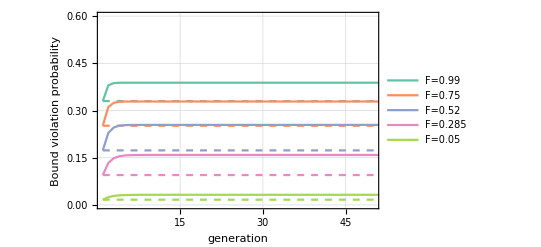

```mathematica
Show[gLines,gSaturation]
```

```mathematica
(* Limit value for pv (fixed point of the recurrence relation) *)
```

```mathematica
sol=Solve[pv==pv/2+(1-pv)*(3*pv^2*F/8+(1-pv^2)*F/3),pv]
```

{{pv→1/3-(36 F+23 F^2)/(3 F (-54 F^2+73 F^3+18 √(144 F^3+285 F^4+152 F^5+54 F^6))^(1/3))+((-54 F^2+73 F^3+18 √(144 F^3+285 F^4+152 F^5+54 F^6))^(1/3))/(3 F)},{pv→1/3+((1+ⅈ √3) (36 F+23 F^2))/(6 F (-54 F^2+73 F^3+18 √(144 F^3+285 F^4+152 F^5+54 F^6))^(1/3))-((1-ⅈ √3) (-54 F^2+73 F^3+18 √(144 F^3+285 F^4+152 F^5+54 F^6))^(1/3))/(6 F)},{pv→1/3+((1-ⅈ √3) (36 F+23 F^2))/(6 F (-54 F^2+73 F^3+18 √(144 F^3+285 F^4+152 F^5+54 F^6))^(1/3))-((1+ⅈ √3) (-54 F^2+73 F^3+18 √(144 F^3+285 F^4+152 F^5+54 F^6))^(1/3))/(6 F)}}

```mathematica
(* dependence on F of the limit value of the violation probability in case of saturation *)
```

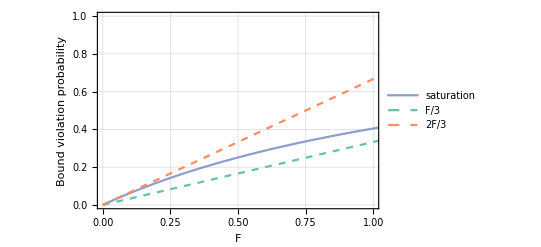

```mathematica
Plot[{pv/.sol[[1]],F/3,2*F/3},{F,0,2},PlotStyle->{RGBColor[colors[[3]]],{Dashed,RGBColor[colors[[1]]]},{Dashed,RGBColor[colors[[2]]]}},PlotRange->{{0,1},{0,1}},Frame->True, FrameLabel->{"F","Bound violation probability"},GridLines->Automatic,PlotLegends->Placed[{"saturation","F/3","2F/3"},{Left,Top}]]
```

```mathematica
pvLimit=Table[pv/.sol[[1]]/.(F->listF[[indF]]),{indF,1,Length[listF]}]
```

{0.0322621,0.160093,0.259025,0.337976,0.4024}